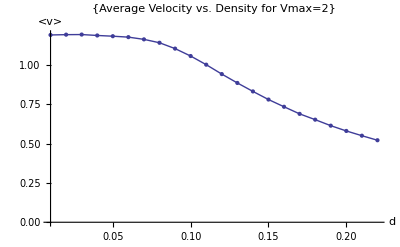

```mathematica
vbar2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vbar.vmax2.txt",{Number,Number}];
a=ListPlot[vbar2,PlotLabel->{"Average Velocity vs. Density for Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
b=ListLinePlot[vbar2,PlotLabel->{"Σ(Fourier Module)^2 vs. k  p=0.8 & d=0.01 Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a,b]
```

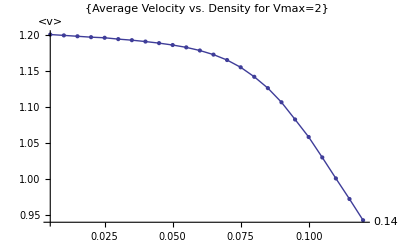

```mathematica
vbar22=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax2/vbar.vmax2.fine2.txt",{Number,Number}];
a2=ListPlot[vbar22,PlotLabel->{"Average Velocity vs. Density for Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
b2=ListLinePlot[vbar22,PlotLabel->{"Average Velocity vs. Density for Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a2,b2]
```

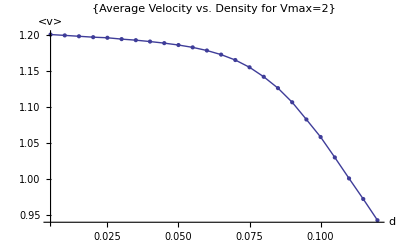

```mathematica
vbar23=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vbar.vmax2.fine2.txt",{Number,Number}];
a3=ListPlot[vbar23,PlotLabel->{"Average Velocity vs. Density for Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
b3=ListLinePlot[vbar23,PlotLabel->{"Average Velocity vs. Density for Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a3,b3]
```

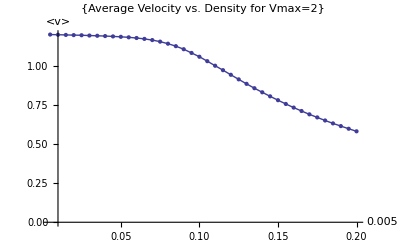

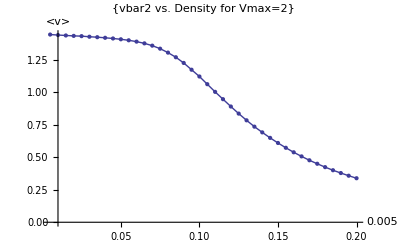

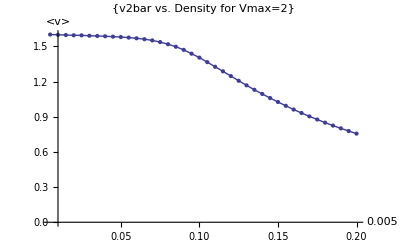

```mathematica
vbar=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax2/vbar.vmax2.fine.txt",{Number,Number}];
a=ListPlot[vbar,PlotLabel->{"Average Velocity vs. Density for Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
b=ListLinePlot[vbar,PlotLabel->{"Average Velocity vs. Density for Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a,b]
vbar2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax2/vbar2.vmax2.fine.txt",{Number,Number}];
a2=ListPlot[vbar2,PlotLabel->{"vbar2 vs. Density for Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
b2=ListLinePlot[vbar2,PlotLabel->{"vbar2 vs. Density for Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a2,b2]
v2bar=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax2/v2bar.vmax2.fine.txt",{Number,Number}];
aa=ListPlot[v2bar,PlotLabel->{"v2bar vs. Density for Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
bb=ListLinePlot[v2bar,PlotLabel->{"v2bar vs. Density for Vmax=2"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[aa,bb]
```

16384. = L

2621 = N

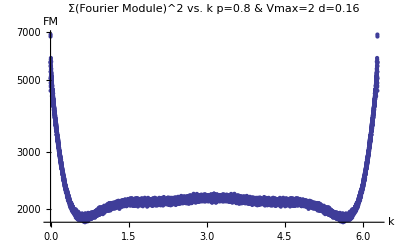

2201.84 = N*(L-N)/(L-1)

2301.08 = Mean of o.7 largest values

3.60728×10^7 = Sum of All L-1 Valus

3.60728×10^7 = N*(L-N)

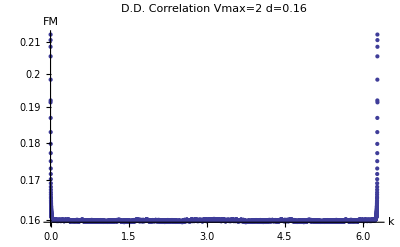

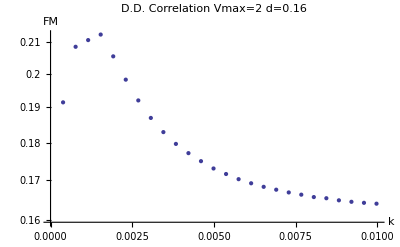

0.159922 = (N-1)/(L-1)

0.159952 = Mean of o.9 largest values

2620. = Sum of All L Valus

2620 = N-1

Values lesser than 2/3*(N-1)/(L-1):

{0,-9.31479×10^-10}

```mathematica
d="0.16";
n=16384.0;
a="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax2/fourier.1d.averaged.d";
b=".p0.8.u.check.v2.txt";
g=".p0.8.u.check.v2.txt";
c=a<>d<>b;
e="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax2/ddensitycorrelation.d";
f=e<>d<>g;
j=StringToStream[d];
o= Read[j,Number];
m=Floor[o*16384];
n "= L"
m  "= N  "
bitF=ReadList[c,{Number,Number}];
bitf2=bitF[[All,2]];
ListLogPlot[bitF,PlotLabel->"Σ(Fourier Module)^2 vs. k  p=0.8 & Vmax=2 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
(n-m)*m/(n-1) "= N*(L-N)/(L-1)"
TrimmedMean[bitf2,{0.3,0}] "= Mean of o.7 largest values"
summ=Sum[bitf2[[i]],{i,1,n-1} ];
N[summ] "= Sum of All L-1 Valus"
m*(n-m) "= N*(L-N)"
Δ=summ-m*(n-m);
density=ReadList[f,{Number,Number}];
density2=density[[All,2]];
ListLogPlot[density,PlotLabel->"D.D. Correlation Vmax=2 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
ListLogPlot[density,PlotLabel->"D.D. Correlation Vmax=2 d="<>  d,AxesLabel->{k,FM},PlotRange->{{0,0.01},Full}]
p=(m-1)/(n-1);
p  "= (N-1)/(L-1)"
TrimmedMean[density2,{0.1,0}] "= Mean of o.9 largest values"
summ2=Sum[density2[[i]],{i,1,n} ];
N[summ2] "= Sum of All L Valus"
m2=m-1;  
m2 "= N-1"
"Values lesser than 2/3*(N-1)/(L-1):"
For[i=0,i<50,i++,
If[density2[[i]]<2*p/3,
Print[{i-1,density2[[i]]}]
]
]
```